r x+x^3-x^5

{{x→0},{x→-(√(1-√(1+4 r)))/(√2)},{x→(√(1-√(1+4 r)))/(√2)},{x→-(√(1+√(1+4 r)))/(√2)},{x→(√(1+√(1+4 r)))/(√2)}}

{r,-1-4 r+√(1+4 r),-1-4 r+√(1+4 r),-1-4 r-√(1+4 r),-1-4 r-√(1+4 r)}

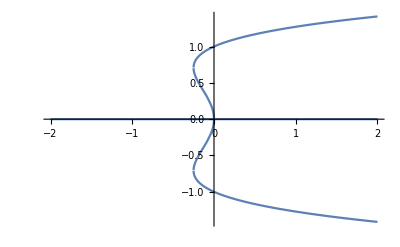

{r,-1-4 r+√(1+4 r),-1-4 r+√(1+4 r),-1-4 r-√(1+4 r),-1-4 r-√(1+4 r)}

-Graphics-

```mathematica
fx = r*x+x^3-x^5
FP=Solve[fx==0,x]
StFP = FullSimplify[D[fx,x]/.FP]
Plot[x/.FP,{r,-2,2}]
```